{a→15.7668}

15.7668 Cos[θ]^2

| Estimate | Standard Error | t-Statistic | P-Value
a | 15.7668 | 13.8778 | 1.13612 | 0.276417

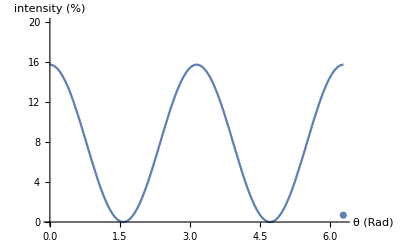

{a→5004.48,b→-77.6588,c→-0.414086}

```mathematica
Clear[a,b,c,θ];

RelAngIntData = {{6.28,0.687},{25.13,0.766},{50.27,1.218},{69.12,3.782},{71.00,4.883},{72.88,6.756},{74.77,10.918},{76.34,24.057},{76.65,31.915},{77.72,149.133},{78.54,35.561},{81.68,7.506},{87.96,2.646},{157.08,0.206}};
HalfplatePolData = {{6.28,0.020},{25.13,0.018},{50.27,0.032},{69.12,0.052},{71.00,0.058},{72.88,0.064},{74.77,0.088},{76.34,0.172},{76.65,0.248},{77.72,1.552},{78.54,2.942},{81.68,3.132},{87.96,3.148},{157.08,3.165}};

FindFit[RelAngIntData,a (Cos[θ])^2,{a},θ]

intensity[θ_]=a (Cos[θ])^2/.%;

nlm=NonlinearModelFit[RelAngIntData,a (Cos[θ])^2,{a},θ];
Normal[nlm]
nlm["ParameterTable"]

Show[Plot[intensity[θ],{θ,0,2 Pi},PlotRange->{0,20}],ListPlot[RelAngIntData],AxesLabel->{"θ (Rad)","intensity (%)"}]
```